# фытотвофытвфыо

## символы и выражения

```mathematica
a = 1
```

1

```mathematica
expressions = {a, b, 1, 1.2, 2+3 ⅈ,2/3,x==y}
```

{1,b,1,1.2,2+3 ⅈ,2/3,x==y}

```mathematica
Head/@expressions
```

{Integer,Symbol,Integer,Real,Complex,Rational,Equal}

```mathematica
Map[Head,expressions]
```

{Integer,Symbol,Integer,Real,Complex,Rational,Equal}

```mathematica
expr = x+y^2+2Sin[x+z^2]
```

x+y^2+2 Sin[x+z^2]

```mathematica
expr//FullForm
```

Plus[x,Power[y,2],Times[2,Sin[Plus[x,Power[z,2]]]]]

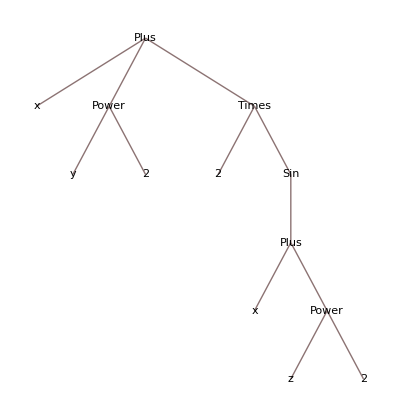

```mathematica
expr//TreeForm
```

```mathematica
Depth[expr]
```

6

```mathematica
Depth@expr
expr//Depth
```

6

6

```mathematica
Level[expr,{5}]⟦1⟧
```

z

```mathematica
Position[expr,z]⟦1⟧
```

{3,2,1,2,1}

```mathematica
expr⟦Sequence@@(Position[expr,z]⟦1⟧)⟧
```

z

```mathematica
expr⟦3,2,1,2,1⟧
```

z

```mathematica
expr = x+y^2+2Sin[x+z^2]
```

x+y^2+2 Sin[x+z^2]

```mathematica
ReplaceAll[expr,x->2]
```

2+y^2+2 Sin[2+z^2]

```mathematica
expr/.{x->2}
```

2+y^2+2 Sin[2+z^2]

```mathematica
π//N
```

3.14159

```mathematica
2/3
```

2/3

```mathematica
Factor[x^4+144]
```

144+x^4

## работа со списками

```mathematica
expressions
```

{1,b,1,1.2,2+3 ⅈ,2/3,x==y}

```mathematica
list =Range[0.2,10,2]
```

{0.2,2.2,4.2,6.2,8.2}

```mathematica
list⟦-1⟧
```

8.2

```mathematica
f[x_]:={x,PrimeQ@x}
```

```mathematica
f/@Range[1,100]
```

{{1,False},{2,True},{3,True},{4,False},{5,True},{6,False},{7,True},{8,False},{9,False},{10,False},{11,True},{12,False},{13,True},{14,False},{15,False},{16,False},{17,True},{18,False},{19,True},{20,False},{21,False},{22,False},{23,True},{24,False},{25,False},{26,False},{27,False},{28,False},{29,True},{30,False},{31,True},{32,False},{33,False},{34,False},{35,False},{36,False},{37,True},{38,False},{39,False},{40,False},{41,True},{42,False},{43,True},{44,False},{45,False},{46,False},{47,True},{48,False},{49,False},{50,False},{51,False},{52,False},{53,True},{54,False},{55,False},{56,False},{57,False},{58,False},{59,True},{60,False},{61,True},{62,False},{63,False},{64,False},{65,False},{66,False},{67,True},{68,False},{69,False},{70,False},{71,True},{72,False},{73,True},{74,False},{75,False},{76,False},{77,False},{78,False},{79,True},{80,False},{81,False},{82,False},{83,True},{84,False},{85,False},{86,False},{87,False},{88,False},{89,True},{90,False},{91,False},{92,False},{93,False},{94,False},{95,False},{96,False},{97,True},{98,False},{99,False},{100,False}}

```mathematica
{#,PrimeQ@#}&/@Range[1,100]
```

{{1,False},{2,True},{3,True},{4,False},{5,True},{6,False},{7,True},{8,False},{9,False},{10,False},{11,True},{12,False},{13,True},{14,False},{15,False},{16,False},{17,True},{18,False},{19,True},{20,False},{21,False},{22,False},{23,True},{24,False},{25,False},{26,False},{27,False},{28,False},{29,True},{30,False},{31,True},{32,False},{33,False},{34,False},{35,False},{36,False},{37,True},{38,False},{39,False},{40,False},{41,True},{42,False},{43,True},{44,False},{45,False},{46,False},{47,True},{48,False},{49,False},{50,False},{51,False},{52,False},{53,True},{54,False},{55,False},{56,False},{57,False},{58,False},{59,True},{60,False},{61,True},{62,False},{63,False},{64,False},{65,False},{66,False},{67,True},{68,False},{69,False},{70,False},{71,True},{72,False},{73,True},{74,False},{75,False},{76,False},{77,False},{78,False},{79,True},{80,False},{81,False},{82,False},{83,True},{84,False},{85,False},{86,False},{87,False},{88,False},{89,True},{90,False},{91,False},{92,False},{93,False},{94,False},{95,False},{96,False},{97,True},{98,False},{99,False},{100,False}}

```mathematica
MapIndexed[{#1,#2}&,expressions]
```

{{1,{1}},{b,{2}},{1,{3}},{1.2,{4}},{2+3 ⅈ,{5}},{2/3,{6}},{x==y,{7}}}

```mathematica
Table[i^2,{i,1,100}]
```

{1,4,9,16,25,36,49,64,81,100,121,144,169,196,225,256,289,324,361,400,441,484,529,576,625,676,729,784,841,900,961,1024,1089,1156,1225,1296,1369,1444,1521,1600,1681,1764,1849,1936,2025,2116,2209,2304,2401,2500,2601,2704,2809,2916,3025,3136,3249,3364,3481,3600,3721,3844,3969,4096,4225,4356,4489,4624,4761,4900,5041,5184,5329,5476,5625,5776,5929,6084,6241,6400,6561,6724,6889,7056,7225,7396,7569,7744,7921,8100,8281,8464,8649,8836,9025,9216,9409,9604,9801,10000}

```mathematica
Table[{i,PrimeQ@i},{i,1,100,4}]
```

{{1,False},{5,True},{9,False},{13,True},{17,True},{21,False},{25,False},{29,True},{33,False},{37,True},{41,True},{45,False},{49,False},{53,True},{57,False},{61,True},{65,False},{69,False},{73,True},{77,False},{81,False},{85,False},{89,True},{93,False},{97,True}}

```mathematica
Table[expressions⟦i⟧^2,{i,1,Length@expressions}]
```

{1,b^2,1,1.44,-5+12 ⅈ,4/9,(x==y)^2}

```mathematica
#^2&/@expressions
```

{1,b^2,1,1.44,-5+12 ⅈ,4/9,(x==y)^2}

```mathematica
list1=RandomInteger[{1,10},10]
```

{10,6,10,5,8,10,3,8,3,6}

```mathematica
list1//Total
```

69

```mathematica
Times@@list1
```

103680000

```mathematica
Select[list1,Mod[#,5]==0&]
```

{10,10,5,10}

```mathematica
Cases[list1,_Integer]
```

{10,6,10,5,8,10,3,8,3,6}

```mathematica
list2 = {2,3,4,5};
list3 = {4,5,6,7};
```

```mathematica
Intersection[list2,list3]
```

{4,5}

```mathematica
Union[list2,list3]
```

{2,3,4,5,6,7}

```mathematica
Join[list2,list3]
```

{2,3,4,5,4,5,6,7}

```mathematica
list2~Join~list2
```

{2,3,4,5,2,3,4,5}

```mathematica
Limit[1/n^2,n->∞]
```

0

```mathematica
Range[]
```

```mathematica
∑_(i=1)^20 1/i^2//N
```

1.59616

```mathematica
1/#^2&/@Range[1,20]//Total
```

17299975731542641/10838475198270720

```mathematica
1/#^2&/@Range[1,200];
```

## Однострочники

```mathematica
2^200-1//FactorInteger//{(#⟦1⟧)^(#⟦2⟧)}&/@#&//Flatten
```

{3,125,11,17,31,41,101,251,401,601,1801,4051,8101,61681,268501,340801,2787601,3173389601}

```mathematica
a = 2^200-1
```

1606938044258990275541962092341162602522202993782792835301375

```mathematica
b = FactorInteger@a
```

{{3,1},{5,3},{11,1},{17,1},{31,1},{41,1},{101,1},{251,1},{401,1},{601,1},{1801,1},{4051,1},{8101,1},{61681,1},{268501,1},{340801,1},{2787601,1},{3173389601,1}}

```mathematica
c = {(#⟦1⟧)^(#⟦2⟧)}&/@b
```

{{3},{125},{11},{17},{31},{41},{101},{251},{401},{601},{1801},{4051},{8101},{61681},{268501},{340801},{2787601},{3173389601}}

```mathematica
d=Flatten[c]
```

{3,125,11,17,31,41,101,251,401,601,1801,4051,8101,61681,268501,340801,2787601,3173389601}

```mathematica
eqn = x^20-3 x^17+x^7+1==0
```

1+x^7-3 x^17+x^20==0

```mathematica
eqn//Solve[#,x]&//Values//Flatten//Select[#,Head[#]==Complex&]&
```

{}

```mathematica
eqn//Solve[#,x]&//Values//Flatten//N//Select[#,Head[#]==Complex&]&//Select[#,Abs[#]<1&]&
```

{-0.907356-0.133137 ⅈ,-0.907356+0.133137 ⅈ,-0.819417-0.509269 ⅈ,-0.819417+0.509269 ⅈ,-0.559062-0.719973 ⅈ,-0.559062+0.719973 ⅈ,-0.262571-0.950152 ⅈ,-0.262571+0.950152 ⅈ,0.12038-0.900976 ⅈ,0.12038+0.900976 ⅈ,0.389224-0.84481 ⅈ,0.389224+0.84481 ⅈ,0.709701-0.625893 ⅈ,0.709701+0.625893 ⅈ,0.835279-0.35531 ⅈ,0.835279+0.35531 ⅈ}

## Написание собственных функций

```mathematica
Sin[60 Degree]
```

(√3)/2

```mathematica
f1[x_,y_]:=If[x<y,x+y,"конь"]
```

```mathematica
f1[3,2]
```

конь

```mathematica
f1[x_Integer]:=PrimeQ[x]
```

```mathematica
f1[x_]:=Plot[Sin[t]+x,{t,-2π,2π}]
```

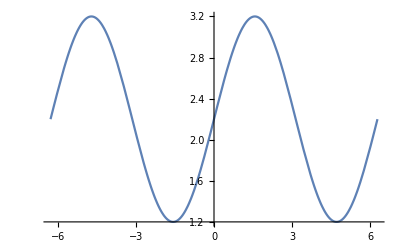

```mathematica
f1[2.2]
```

```mathematica
??f1
```

```mathematica
f2[x_]:=With[{a = Sin[x]},a^2]
```

```mathematica
f2[π/2]
```

1

```mathematica
fib[1]:=1;
fib[2]:=1;
fib[n_]:=fib[n-1]+fib[n-2]
```

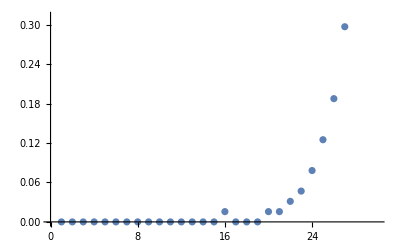

```mathematica
ListPlot[{#,Timing[fib[#]]⟦1⟧}&/@Range[30]]
```

```mathematica
Timing[fib[4]]
```

{0.,3}

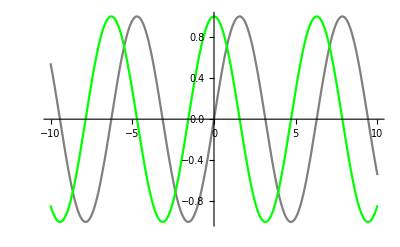

```mathematica
Plot[{Sin[x],Cos[x]},{x,-10,10},PlotStyle->{Gray,Green}]
```

```mathematica
Manipulate[Graphics[{Red,PointSize@0.02,Point[{1,1}],Black,Line[{{1,1},{2,a}}]},PlotRange->{{0,10},{0,10}}],{a,2,10}]
```